# G3Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]+5]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]-4;;Dimensions[data][[1]]]];
```

# G3CoreWH + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3CoreWH.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[1;;LengthWhile[Transpose[data][[1]],#<50.&]+31]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]-30;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-30]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-29]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-28]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-27]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-26]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-25]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-24]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-23]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-22]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-21]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-20]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-19]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-18]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-17]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-16]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-15]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-14]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-13]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-12]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-11]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-10]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-9]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-8]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-7]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-6]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-5]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={dataOuterCore[[1]],dataOuterCore[[2]],dataOuterCore[[3]],dataOuterCore[[4]],dataOuterCore[[5]],dataOuterCore[[6]],dataOuterCore[[7]],dataOuterCore[[8]],dataOuterCore[[9]],dataOuterCore[[10]],dataOuterCore[[11]],dataOuterCore[[12]],dataOuterCore[[13]],dataOuterCore[[14]],dataOuterCore[[15]],dataOuterCore[[16]],dataOuterCore[[17]],dataOuterCore[[18]],dataOuterCore[[19]],dataOuterCore[[20]],dataOuterCore[[21]],dataOuterCore[[22]],dataOuterCore[[23]],dataOuterCore[[24]],dataOuterCore[[25]],dataOuterCore[[26]],dataOuterCore[[27]],dataOuterCore[[28]],dataOuterCore[[29]],dataOuterCore[[30]]};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

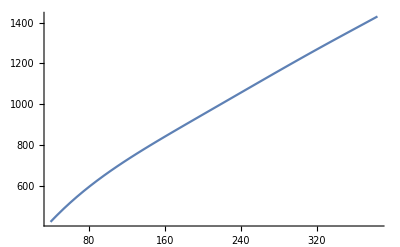

190.572+6.91982 P0-0.0306383 P0^2+0.0000986569 P0^3-1.04354×10^-7 P0^4-1.16501×10^-10 P0^5+2.35784×10^-13 P0^6

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]}]
fitInnerCoreWH=fitted
```

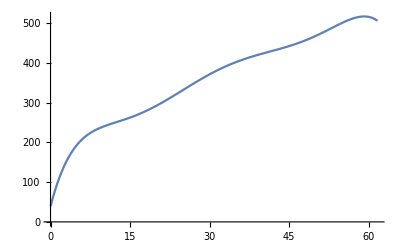

39.2027+51.293 P0-5.34397 P0^2+0.291412 P0^3-0.0079031 P0^4+0.00010365 P0^5-5.24731×10^-7 P0^6

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]}]
fitOuterCoreWH=fitted
```

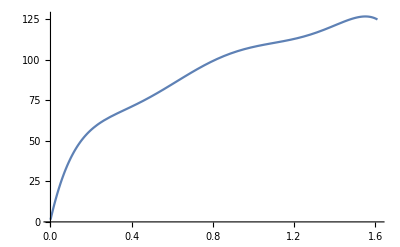

1.22313+545.007 P0-1980.94 P0^2+3952.28 P0^3-4016.12 P0^4+1986.62 P0^5-380.047 P0^6

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]}]
fitInnerCrustWH=fitted
```

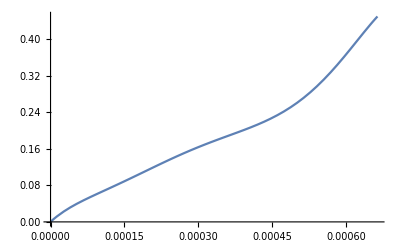

0.000206631+985.755 P0-6.45265×10^6 P0^2+4.04549×10^10 P0^3-1.2422×10^14 P0^4+1.76549×10^17 P0^5-9.15294×10^19 P0^6

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]}]
fitOuterCrustWH=fitted
```

# G3CoreWHSS

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3CoreWHSS.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[1;;LengthWhile[Transpose[data][[1]],#<50.&]+31]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]-30;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-30]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-29]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-28]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-27]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-26]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-25]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-24]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-23]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-22]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-21]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-20]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-19]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-18]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-17]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-16]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-15]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-14]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-13]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-12]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-11]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-10]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-9]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-8]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-7]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-6]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-5]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={dataOuterCore[[1]],dataOuterCore[[2]],dataOuterCore[[3]],dataOuterCore[[4]],dataOuterCore[[5]],dataOuterCore[[6]],dataOuterCore[[7]],dataOuterCore[[8]],dataOuterCore[[9]],dataOuterCore[[10]],dataOuterCore[[11]],dataOuterCore[[12]],dataOuterCore[[13]],dataOuterCore[[14]],dataOuterCore[[15]],dataOuterCore[[16]],dataOuterCore[[17]],dataOuterCore[[18]],dataOuterCore[[19]],dataOuterCore[[20]],dataOuterCore[[21]],dataOuterCore[[22]],dataOuterCore[[23]],dataOuterCore[[24]],dataOuterCore[[25]],dataOuterCore[[26]],dataOuterCore[[27]],dataOuterCore[[28]],dataOuterCore[[29]],dataOuterCore[[30]]};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

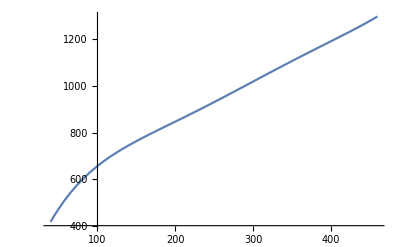

110.597+9.94737 P0-0.0660759 P0^2+0.000258151 P0^3-5.08599×10^-7 P0^4+4.57459×10^-10 P0^5-1.24843×10^-13 P0^6

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]}]
fitInnerCoreWHSS=fitted
```

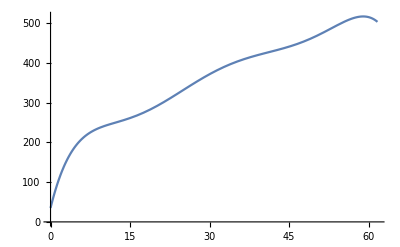

35.0383+53.9768 P0-5.74883 P0^2+0.316176 P0^3-0.00862202 P0^4+0.000113535 P0^5-5.76553×10^-7 P0^6

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]}]
fitOuterCoreWHSS=fitted
```

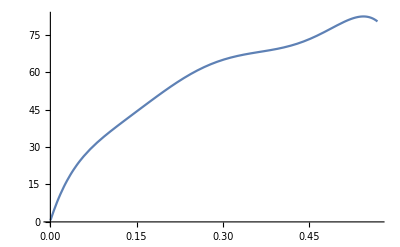

0.461901+713.665 P0-6542.45 P0^2+39923.8 P0^3-126795. P0^4+193534. P0^5-112410. P0^6

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]}]
fitInnerCrustWHSS=fitted
```

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]}]
fitOuterCrustWHSS=fitted
```

-Graphics-

0.000206631+985.755 P0-6.45265×10^6 P0^2+4.04549×10^10 P0^3-1.2422×10^14 P0^4+1.76549×10^17 P0^5-9.15294×10^19 P0^6

# G3CoreWoutH

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3CoreWoutH.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[1;;LengthWhile[Transpose[data][[1]],#<50.&]+31]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]-30;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-30]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-29]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-28]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-27]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-26]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-25]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-24]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-23]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-22]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-21]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-20]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-19]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-18]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-17]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-16]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-15]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-14]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-13]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-12]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-11]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-10]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-9]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-8]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-7]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-6]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-5]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={dataOuterCore[[1]],dataOuterCore[[2]],dataOuterCore[[3]],dataOuterCore[[4]],dataOuterCore[[5]],dataOuterCore[[6]],dataOuterCore[[7]],dataOuterCore[[8]],dataOuterCore[[9]],dataOuterCore[[10]],dataOuterCore[[11]],dataOuterCore[[12]],dataOuterCore[[13]],dataOuterCore[[14]],dataOuterCore[[15]],dataOuterCore[[16]],dataOuterCore[[17]],dataOuterCore[[18]],dataOuterCore[[19]],dataOuterCore[[20]],dataOuterCore[[21]],dataOuterCore[[22]],dataOuterCore[[23]],dataOuterCore[[24]],dataOuterCore[[25]],dataOuterCore[[26]],dataOuterCore[[27]],dataOuterCore[[28]],dataOuterCore[[29]],dataOuterCore[[30]]};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

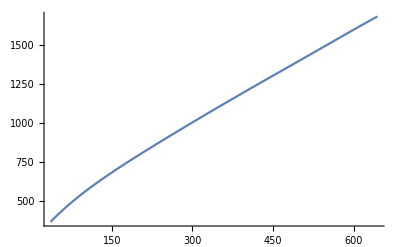

225.602+4.47966 P0-0.0157054 P0^2+0.0000562748 P0^3-1.14736×10^-7 P0^4+1.22327×10^-10 P0^5-5.27224×10^-14 P0^6

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]}]
fitInnerCoreWoutH=fitted
```

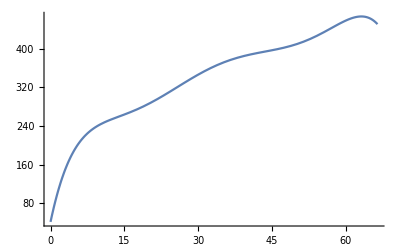

41.111+48.1974 P0-4.60197 P0^2+0.23133 P0^3-0.00585987 P0^4+0.0000720405 P0^5-3.41863×10^-7 P0^6

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]}]
fitOuterCoreWoutH=fitted
```

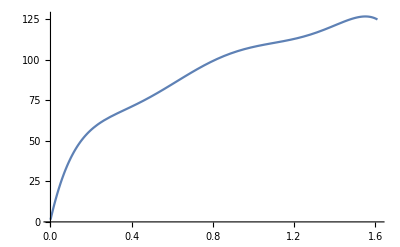

1.22338+544.966 P0-1980.44 P0^2+3950.4 P0^3-4013.3 P0^4+1984.79 P0^5-379.616 P0^6

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]}]
fitInnerCrustWoutH=fitted
```

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]}]
fitOuterCrustWoutH=fitted
```

-Graphics-

0.000206631+985.755 P0-6.45265×10^6 P0^2+4.04549×10^10 P0^3-1.2422×10^14 P0^4+1.76549×10^17 P0^5-9.15294×10^19 P0^6

# G3CoreWoutHSS

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3CoreWoutHSS.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[1;;LengthWhile[Transpose[data][[1]],#<50.&]+31]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]-30;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-30]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-29]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-28]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-27]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-26]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-25]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-24]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-23]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-22]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-21]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-20]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-19]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-18]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-17]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-16]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-15]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-14]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-13]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-12]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-11]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-10]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-9]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-8]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-7]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-6]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-5]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={dataOuterCore[[1]],dataOuterCore[[2]],dataOuterCore[[3]],dataOuterCore[[4]],dataOuterCore[[5]],dataOuterCore[[6]],dataOuterCore[[7]],dataOuterCore[[8]],dataOuterCore[[9]],dataOuterCore[[10]],dataOuterCore[[11]],dataOuterCore[[12]],dataOuterCore[[13]],dataOuterCore[[14]],dataOuterCore[[15]],dataOuterCore[[16]],dataOuterCore[[17]],dataOuterCore[[18]],dataOuterCore[[19]],dataOuterCore[[20]],dataOuterCore[[21]],dataOuterCore[[22]],dataOuterCore[[23]],dataOuterCore[[24]],dataOuterCore[[25]],dataOuterCore[[26]],dataOuterCore[[27]],dataOuterCore[[28]],dataOuterCore[[29]],dataOuterCore[[30]]};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

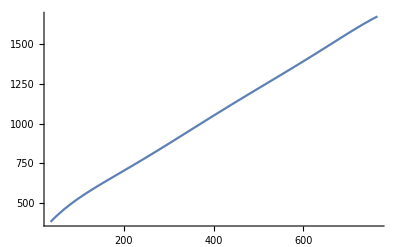

252.882+4.07561 P0-0.0191832 P0^2+0.0000745368 P0^3-1.48601×10^-7 P0^4+1.46764×10^-10 P0^5-5.68597×10^-14 P0^6

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]}]
fitInnerCoreWoutHSS=fitted
```

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]}]
fitOuterCoreWoutHSS=fitted
```

-Graphics-

41.111+48.1974 P0-4.60197 P0^2+0.23133 P0^3-0.00585987 P0^4+0.0000720405 P0^5-3.41863×10^-7 P0^6

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]}]
fitInnerCrustWoutHSS=fitted
```

-Graphics-

1.22338+544.966 P0-1980.44 P0^2+3950.4 P0^3-4013.3 P0^4+1984.79 P0^5-379.616 P0^6

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]}]
fitOuterCrustWoutHSS=fitted
```

-Graphics-

0.000206631+985.755 P0-6.45265×10^6 P0^2+4.04549×10^10 P0^3-1.2422×10^14 P0^4+1.76549×10^17 P0^5-9.15294×10^19 P0^6

# Cek hasil

## EoS WH

190.572+6.91982 P0-0.0306383 P0^2+0.0000986569 P0^3-1.04354×10^-7 P0^4-1.16501×10^-10 P0^5+2.35784×10^-13 P0^6

39.2027+51.293 P0-5.34397 P0^2+0.291412 P0^3-0.0079031 P0^4+0.00010365 P0^5-5.24731×10^-7 P0^6

1.22313+545.007 P0-1980.94 P0^2+3952.28 P0^3-4016.12 P0^4+1986.62 P0^5-380.047 P0^6

0.000206631+985.755 P0-6.45265×10^6 P0^2+4.04549×10^10 P0^3-1.2422×10^14 P0^4+1.76549×10^17 P0^5-9.15294×10^19 P0^6

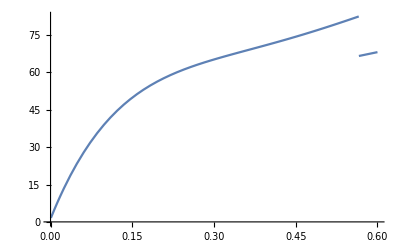

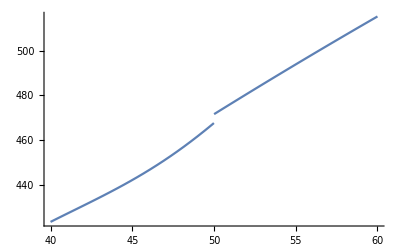

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreWH
FED2[P0_]=fitOuterCoreWH
FED3[P0_]=fitInnerCrustWH
FED4[P0_]=fitOuterCrustWH
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,40,60},PlotRange->All]
```

## EoS WHSS

110.597+9.94737 P0-0.0660759 P0^2+0.000258151 P0^3-5.08599×10^-7 P0^4+4.57459×10^-10 P0^5-1.24843×10^-13 P0^6

35.0383+53.9768 P0-5.74883 P0^2+0.316176 P0^3-0.00862202 P0^4+0.000113535 P0^5-5.76553×10^-7 P0^6

0.461901+713.665 P0-6542.45 P0^2+39923.8 P0^3-126795. P0^4+193534. P0^5-112410. P0^6

0.000206631+985.755 P0-6.45265×10^6 P0^2+4.04549×10^10 P0^3-1.2422×10^14 P0^4+1.76549×10^17 P0^5-9.15294×10^19 P0^6

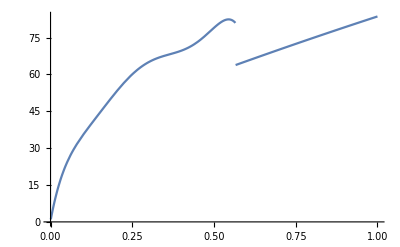

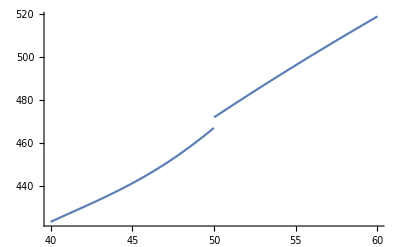

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreWHSS
FED2[P0_]=fitOuterCoreWHSS
FED3[P0_]=fitInnerCrustWHSS
FED4[P0_]=fitOuterCrustWHSS
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,1}]
Plot[ϵ[p],{p,40,60},PlotRange->All]
```

## EoS WoutH

225.602+4.47966 P0-0.0157054 P0^2+0.0000562748 P0^3-1.14736×10^-7 P0^4+1.22327×10^-10 P0^5-5.27224×10^-14 P0^6

41.111+48.1974 P0-4.60197 P0^2+0.23133 P0^3-0.00585987 P0^4+0.0000720405 P0^5-3.41863×10^-7 P0^6

1.22338+544.966 P0-1980.44 P0^2+3950.4 P0^3-4013.3 P0^4+1984.79 P0^5-379.616 P0^6

0.000206631+985.755 P0-6.45265×10^6 P0^2+4.04549×10^10 P0^3-1.2422×10^14 P0^4+1.76549×10^17 P0^5-9.15294×10^19 P0^6

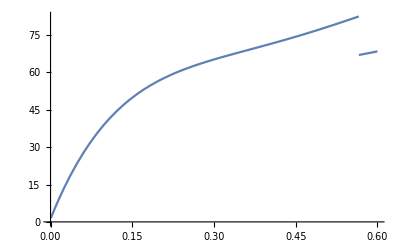

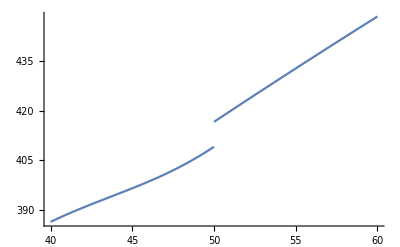

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreWoutH
FED2[P0_]=fitOuterCoreWoutH
FED3[P0_]=fitInnerCrustWoutH
FED4[P0_]=fitOuterCrustWoutH
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,40,60},PlotRange->All]
```

## EoS WoutHSS

252.882+4.07561 P0-0.0191832 P0^2+0.0000745368 P0^3-1.48601×10^-7 P0^4+1.46764×10^-10 P0^5-5.68597×10^-14 P0^6

41.111+48.1974 P0-4.60197 P0^2+0.23133 P0^3-0.00585987 P0^4+0.0000720405 P0^5-3.41863×10^-7 P0^6

1.22338+544.966 P0-1980.44 P0^2+3950.4 P0^3-4013.3 P0^4+1984.79 P0^5-379.616 P0^6

0.000206631+985.755 P0-6.45265×10^6 P0^2+4.04549×10^10 P0^3-1.2422×10^14 P0^4+1.76549×10^17 P0^5-9.15294×10^19 P0^6

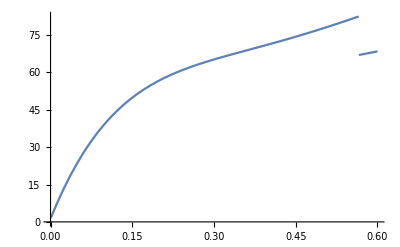

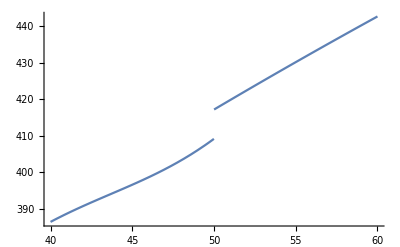

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreWoutHSS
FED2[P0_]=fitOuterCoreWoutHSS
FED3[P0_]=fitInnerCrustWoutHSS
FED4[P0_]=fitOuterCrustWoutHSS
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,0.6},PlotRange->All]
Plot[ϵ[p],{p,40,60},PlotRange->All]
```

# Hasil Akhir

## EoS WH

```mathematica
fitInnerCoreWH//FortranForm
```

190.57179270587372 + 6.9198169233699565*P0 - 
     -  0.030638310798671707*P0**2 + 
     -  0.00009865686204019007*P0**3 - 
     -  1.043538675041286e-7*P0**4 - 
     -  1.16501148609768e-10*P0**5 + 
     -  2.3578406509208834e-13*P0**6

```mathematica
fitOuterCoreWH//FortranForm
```

39.20272622960714 + 51.29304707677782*P0 - 
     -  5.34397372585973*P0**2 + 0.2914116362267377*P0**3 - 
     -  0.007903097722890455*P0**4 + 
     -  0.00010364988272561263*P0**5 - 
     -  5.247311539724067e-7*P0**6

```mathematica
fitInnerCrustWH//FortranForm
```

1.2231346546555182 + 545.0070634398301*P0 - 
     -  1980.9424258620131*P0**2 + 3952.283402782933*P0**3 - 
     -  4016.1166348731576*P0**4 + 1986.61817154754*P0**5 - 
     -  380.0471984463401*P0**6

```mathematica
fitOuterCrustWH//FortranForm
```

0.00020663104786834376 + 985.755096204799*P0 - 
     -  6.452649548410587e6*P0**2 + 
     -  4.045493650683301e10*P0**3 - 
     -  1.2422017897553961e14*P0**4 + 
     -  1.7654930953548538e17*P0**5 - 
     -  9.152941701213566e19*P0**6

## EoS WHSS

```mathematica
fitInnerCoreWHSS//FortranForm
```

110.59668603860578 + 9.947372455335096*P0 - 
     -  0.06607587084264362*P0**2 + 
     -  0.0002581513410710967*P0**3 - 
     -  5.085987931909115e-7*P0**4 + 
     -  4.574589815066655e-10*P0**5 - 
     -  1.2484341956795887e-13*P0**6

```mathematica
fitOuterCoreWHSS//FortranForm
```

35.038327040450326 + 53.97681811284042*P0 - 
     -  5.748832393864667*P0**2 + 0.3161760763740174*P0**3 - 
     -  0.008622017916962165*P0**4 + 
     -  0.00011353471751418895*P0**5 - 
     -  5.765532639807618e-7*P0**6

```mathematica
fitInnerCrustWHSS//FortranForm
```

0.4619014372215317 + 713.6650354810016*P0 - 
     -  6542.451262273231*P0**2 + 39923.80092926201*P0**3 - 
     -  126795.44184610137*P0**4 + 193533.92226133795*P0**5 - 
     -  112410.42490096122*P0**6

```mathematica
fitOuterCrustWHSS//FortranForm
```

0.00020663104786834376 + 985.755096204799*P0 - 
     -  6.452649548410587e6*P0**2 + 
     -  4.045493650683301e10*P0**3 - 
     -  1.2422017897553961e14*P0**4 + 
     -  1.7654930953548538e17*P0**5 - 
     -  9.152941701213566e19*P0**6

## EoS WoutH

```mathematica
fitInnerCoreWoutH//FortranForm
```

225.60241382739116 + 4.479661681241633*P0 - 
     -  0.015705385083576447*P0**2 + 
     -  0.00005627482511793866*P0**3 - 
     -  1.1473609048384772e-7*P0**4 + 
     -  1.2232653727189085e-10*P0**5 - 
     -  5.2722379726588064e-14*P0**6

```mathematica
fitOuterCoreWoutH//FortranForm
```

41.11101322904766 + 48.19741000043469*P0 - 
     -  4.601974117448184*P0**2 + 0.23132980230856232*P0**3 - 
     -  0.005859871848140427*P0**4 + 
     -  0.0000720405141994315*P0**5 - 
     -  3.4186262510670086e-7*P0**6

```mathematica
fitInnerCrustWoutH//FortranForm
```

1.223376300977984 + 544.9657700017343*P0 - 
     -  1980.438496946232*P0**2 + 3950.4000383350876*P0**3 - 
     -  4013.3021087180173*P0**4 + 1984.789579880287*P0**5 - 
     -  379.6159817328029*P0**6

```mathematica
fitOuterCrustWoutH//FortranForm
```

0.00020663104786834376 + 985.755096204799*P0 - 
     -  6.452649548410587e6*P0**2 + 
     -  4.045493650683301e10*P0**3 - 
     -  1.2422017897553961e14*P0**4 + 
     -  1.7654930953548538e17*P0**5 - 
     -  9.152941701213566e19*P0**6

## EoS WoutHSS

```mathematica
fitInnerCoreWoutHSS//FortranForm
```

252.88196462195216 + 4.075613163297706*P0 - 
     -  0.019183242741940772*P0**2 + 
     -  0.00007453678281005214*P0**3 - 
     -  1.4860141022283878e-7*P0**4 + 
     -  1.4676397960032589e-10*P0**5 - 
     -  5.685967947432084e-14*P0**6

```mathematica
fitOuterCoreWoutHSS//FortranForm
```

41.11101322904766 + 48.19741000043469*P0 - 
     -  4.601974117448184*P0**2 + 0.23132980230856232*P0**3 - 
     -  0.005859871848140427*P0**4 + 
     -  0.0000720405141994315*P0**5 - 
     -  3.4186262510670086e-7*P0**6

```mathematica
fitInnerCrustWoutHSS//FortranForm
```

1.223376300977984 + 544.9657700017343*P0 - 
     -  1980.438496946232*P0**2 + 3950.4000383350876*P0**3 - 
     -  4013.3021087180173*P0**4 + 1984.789579880287*P0**5 - 
     -  379.6159817328029*P0**6

```mathematica
fitOuterCrustWoutHSS//FortranForm
```

0.00020663104786834376 + 985.755096204799*P0 - 
     -  6.452649548410587e6*P0**2 + 
     -  4.045493650683301e10*P0**3 - 
     -  1.2422017897553961e14*P0**4 + 
     -  1.7654930953548538e17*P0**5 - 
     -  9.152941701213566e19*P0**6

# Naive fitting

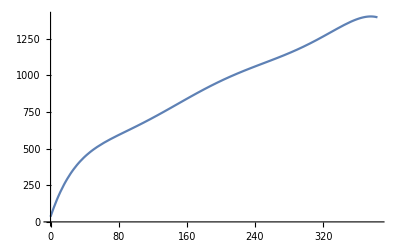

35.38875313226208 + 17.24847480749493*P0 - 
     -  0.2448168236745378*P0**2 + 
     -  0.0020467888116389543*P0**3 - 
     -  8.782852352403798e-6*P0**4 + 
     -  1.8483442745836703e-8*P0**5 - 
     -  1.5101080861937848e-11*P0**6

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
datacrust=data;
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3CoreWH.dat"}];
data=ReadList[fname,{Number,Number}];
datacrustcore=Join[datacrust,data];
fitted=Fit[datacrustcore,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[datacrustcore][[1]]],Max[Transpose[datacrustcore][[1]]]}]
fitalldataWH=fitted;
fitalldataWH//FortranForm
```

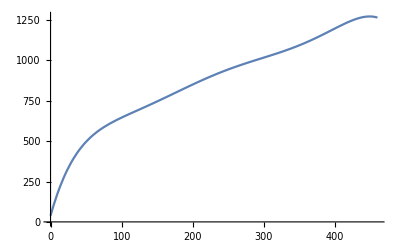

38.50467799910013 + 15.685128505945936*P0 - 
     -  0.18084960995412983*P0**2 + 
     -  0.001196104238390078*P0**3 - 
     -  4.1500340315907694e-6*P0**4 + 
     -  7.155178985377673e-9*P0**5 - 
     -  4.823487894465202e-12*P0**6

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
datacrust=data;
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3CoreWHSS.dat"}];
data=ReadList[fname,{Number,Number}];
datacrustcore=Join[datacrust,data];
fitted=Fit[datacrustcore,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[datacrustcore][[1]]],Max[Transpose[datacrustcore][[1]]]}]
fitalldataWHSS=fitted;
fitalldataWHSS//FortranForm
```

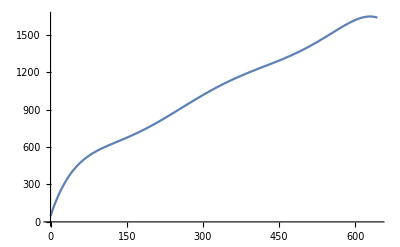

47.90062932721776 + 12.225768076115184*P0 - 
     -  0.11457226593449464*P0**2 + 
     -  0.000600013940954589*P0**3 - 
     -  1.569481469885387e-6*P0**4 + 
     -  1.9891120510167144e-9*P0**5 - 
     -  9.729037482565278e-13*P0**6

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
datacrust=data;
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3CoreWoutH.dat"}];
data=ReadList[fname,{Number,Number}];
datacrustcore=Join[datacrust,data];
fitted=Fit[datacrustcore,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[datacrustcore][[1]]],Max[Transpose[datacrustcore][[1]]]}]
fitalldataWoutH=fitted;
fitalldataWoutH//FortranForm
```

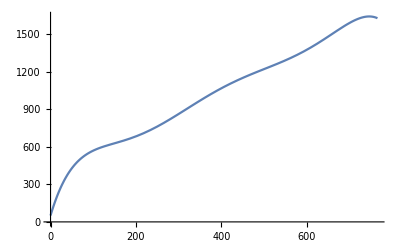

51.03925729566848 + 11.483991820732193*P0 - 
     -  0.09784975654592297*P0**2 + 
     -  0.00043469461945059353*P0**3 - 
     -  9.522102958267907e-7*P0**4 + 
     -  1.0081617266058726e-9*P0**5 - 
     -  4.119793693767378e-13*P0**6

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
datacrust=data;
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3CoreWoutHSS.dat"}];
data=ReadList[fname,{Number,Number}];
datacrustcore=Join[datacrust,data];
fitted=Fit[datacrustcore,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[datacrustcore][[1]]],Max[Transpose[datacrustcore][[1]]]}]
fitalldataWoutHSS=fitted;
fitalldataWoutHSS//FortranForm
```